# Computations for AD

This notebook contains the numerical computations used in Chapter 4 of the thesis.

## Case with two polynomials

Consider the functions A_1 and A_2 associated with the polynomials F_1(X,Y)=X-Y and F_2(X,Y)=X+Y and the convex combination P. The weight l varies in [0,1].

```mathematica
Clear[A1,A2,P,l0,heightBound1]
```

```mathematica
A1[u_]:=Log[8/(1-u)]
A2[u_]:=Log[2/(1+u)]
P[u_,l_]:=l A1[u]+(1-l)A2[u]
```

Compute the derivative of P with respect to u and the critical value u_0.

```mathematica
D[P[u,l],u]
u0=SolveValues[D[P[u,l],u]==0,u][[1]];
```

l/(1-u)-(1-l)/(1+u)

Compute the second derivative of P with respect to u and check that it is positive in (-1,1).

```mathematica
D[P[u,l],{u,2}]
```

l/(1-u)^2+(1-l)/(1+u)^2

```mathematica
FullSimplify[D[P[u,l],{u,2}]>0,Assumptions->-1<u<1&&0<=l<=1]
```

True

For  0<l<1, the function P(u,l)is strictly convex on (-1,1). Hence, its critical point is its global minimum. We then maximize P(u_0,l) with respect to l. 
We compute its first derivative in l and compute the critical value l_0.

```mathematica
D[P[u0,l],l]
```

-1+(2 (1-l))/(2-2 l)-Log[2/(2-2 l)]+Log[4/l]

```mathematica
l0=SolveValues[D[P[1-2l,l],l]==0,l][[1]]
```

4/5

Check that the second derivative is negative.

```mathematica
D[P[u0,l],{l,2}]//Apart
```

1/(-1+l)-1/l

```mathematica
FullSimplify[D[P[u0,l],{l,2}]<0,Assumptions->0<l<1]
```

True

Compute sup_(l∈[0,1]) inf_(u∈[-1,1]) P[u,l] and the height bound.

```mathematica
P[u0/.{l->l0},l0]
```

Log[5]

```mathematica
heightBound1=P[u0/.{l->l0},l0]/12
```

Log[5]/12

## Case with three polynomials

Consider the function A_3 associated with the polynomial F_3(X,Y)=5 X^2+6XY+5 Y^2 and the convex combination Q of A_1, A_2, and A_3. The weights l_1 and l_2 are nonnegative and such that l_1+l_2≤1.

```mathematica
Clear[A3,Q,dQdu,u1,Q1,Q2,eps,MaximizingF,heightBound2,u11,u12]
```

```mathematica
A3[u_]:=Log[8/Abs[5u + 3]]
Q[u_,l1_,l2_]:=l1 A1[u]+l2 A2[u]+(1-l1-l2)A3[u]
```

We compute the critical points u_1 and u_2 of Q on the intervals (-1,-3/5) and (-3/5,1).

```mathematica
dQdu=D[Q[u,l1,l2],u]//ComplexExpand (*ComplexExpand avoids issues with the derivative of Abs*)
```

l1/(1-u)-l2/(1+u)-5/(3+5 u)+(5 l1)/(3+5 u)+(5 l2)/(3+5 u)

```mathematica
u1=Solve[dQdu==0,u]
```

{{u→1/5 (-4 l1+l2-√(25-40 l1+16 l1^2-10 l2-8 l1 l2+l2^2))},{u→1/5 (-4 l1+l2+√(25-40 l1+16 l1^2-10 l2-8 l1 l2+l2^2))}}

```mathematica
Q1[l1_,l2_]:=Q[u/.u1[[1]],l1,l2];
Q2[l1_,l2_]:=Q[u/.u1[[2]],l1,l2];
```

To numerically compute sup_(l_1≥0,l_2≥0,l_1+l_2≤1) min{Q[u_1,l_1,l_2],Q[u_2,l_1,l_2]}, first define the function min{Q[u_1,l_1,l_2],Q[u_2,l_1,l_2]}. The parameter eps is introduced to avoid convergence issues.

```mathematica
eps=10^-16;
```

```mathematica
MaximizingF[l1_?NumericQ,l2_?NumericQ]:=
If[
l1>=eps&&l2>=eps&&l1+l2<=1-eps,
Min[Q1[l1,l2],Q2[l1,l2]],-1
];
```

Compute the height lower bound and the optima weights attaining it.

```mathematica
heightBound2=
NMaximize[
{
MaximizingF[l1,l2],
{l1>=eps,l2>=eps,l1+l2<=1-eps}
},
{l1,l2},
MaxIterations->1000,
WorkingPrecision->50,
AccuracyGoal->25
];heightBound2
```

{1.6823461190590914361922170690270219640199633241724,{l1→0.71928667136127294289150824520156509525425350978239,l2→0.14749386462610026647490856386182079201540064811466}}

We have the following lower bound for the height

```mathematica
heightBound2[[1]]/12
```

0.14019550992159095301601808908558516366833027701437

The bound is attained at the points u_(1,1) and u_(1,2).

```mathematica
u11=u/.u1[[1]]/.heightBound2[[2]]
```

-0.8428884077371349500118345962070513648764899949248

```mathematica
u12=u/.u1[[2]]/.heightBound2[[2]]
```

-0.248972720590461652024615170570724470724155361481

## Case with four polynomials

### Finding the fourth polynomial

Consider the polynomial B[u,a,b]=a(u-1)^2+8b(u-1)+64. We compute the real values aa and bb for which B[u_(1,1),aa,bb]=B[u_(1,2),aa,bb]=0.

```mathematica
Clear[B,L,aa,bb,a1,b1,r,fig]
```

```mathematica
B[u_,a_,b_]:=a(u-1)^2+8b(u-1)+64
```

```mathematica
L=SolveValues[B[u11,a,b]==0&&B[u12,a,b]==0,{a,b}][[1]]
```

{27.80532546522704608983534111449235315794773167752,10.74627562080411870504402927480427823570447571279}

```mathematica
aa=L[[1]]
```

27.80532546522704608983534111449235315794773167752

```mathematica
bb=L[[2]]
```

10.74627562080411870504402927480427823570447571279

Consider a_1 and b_1 the nearest integers to aa and bb, respectively. We look for integers a and b such that |B[u_(1,1),a,b]|≤R and |B[u_(1,2),a,b]|≤R, where r=Max[|B[u_(1,1),a,b]|,|B[u_(1,2),a,b]|].

```mathematica
a1=Round[aa]
```

28

```mathematica
b1=Round[bb]
```

11

```mathematica
r=Max[Abs[B[u11,a1,b1]],Abs[B[u12,a1,b1]]]
```

3.079524746454324002632410850925859826932335763

```mathematica
Reduce[Abs[B[u11,a2,b2]]<=r&&Abs[B[u12,a2,b2]]<=r,{a2,b2},Integers]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(a2==24&&b2==10)||(a2==29&&b2==11)||(a2==34&&b2==12)

The feasible region together with the relevant integer points are shown below.

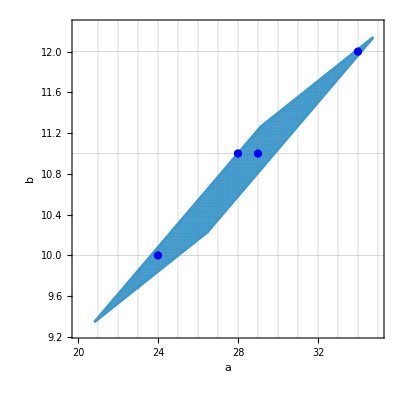

```mathematica
fig=RegionPlot[
Abs[B[u11,a,b]]<r&&Abs[B[u12,a,b]]<r,
{a,20,35},
{b,9.25,12.25},

PlotPoints->400,
GridLines->{Range[21,35,1],Range[9,12,1]},
FrameLabel->{a,b},

PlotRange->{{20,35},{9.25,12.25}},
PlotRangeClipping->False,
ImagePadding->30,

Epilog->{
Blue,
PointSize[0.015],
Point[{{24,10},{29,11},{34,12},{28,11}}]
}(*Points are in Epilog to avoid rendering issues when exporting into EPS*)
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"picture.eps"}],fig,"EPS"];
```

Among the candidate integer pairs, the pair(29,11) minimizes  Max[|B[u_(1,1),a,b]|,|B[u_(1,2),a,b]|].

```mathematica
Max[Abs[B[u11,24,10]],Abs[B[u12,24,10]]]
```

1.9213682180448946308818817405972575196630992023

```mathematica
Max[Abs[B[u11,28,11]],Abs[B[u12,28,11]]]
```

3.079524746454324002632410850925859826932335763

```mathematica
Max[Abs[B[u11,29,11]],Abs[B[u12,29,11]]]
```

0.67154656536558302413255833800932089438719468786

```mathematica
Max[Abs[B[u11,34,12]],Abs[B[u12,34,12]]]
```

2.8636640461935792827374837246071110516738035931

### Computing the bound

Consider the polynomial F(X,Y)=29 X^4+60 X^3 Y+78 X^2 Y^2+60 XY^3+29 Y^4 and the associated function A_4.

```mathematica
Clear[A4,R,D1,poly,heightBound3]
```

```mathematica
A4[u_]:=1/2 Log[64/Abs[29 u^2+30u+5]]
```

Consider the convex combination R of A_1,...,A_4

```mathematica
R[u_,l1_,l2_,l3_]:=l1 A1[u]+l2 A2[u]+l3 A3[u]+(1-l1-l2-l3)A4[u];R[u,l1,l2,l3]
```

l1 Log[8/(1-u)]+l2 Log[2/(1+u)]+l3 Log[8/Abs[3+5 u]]+1/2 (1-l1-l2-l3) Log[64/Abs[5+30 u+29 u^2]]

Compute the first and second derivatives of R.

```mathematica
D1=D[R[u,l1,l2,l3],u]//ComplexExpand
```

l1/(1-u)-l2/(1+u)-(5 l3)/(3+5 u)-15/(5+30 u+29 u^2)+(15 l1)/(5+30 u+29 u^2)+(15 l2)/(5+30 u+29 u^2)+(15 l3)/(5+30 u+29 u^2)-(29 u)/(5+30 u+29 u^2)+(29 l1 u)/(5+30 u+29 u^2)+(29 l2 u)/(5+30 u+29 u^2)+(29 l3 u)/(5+30 u+29 u^2)

```mathematica
D[R[u,l1,l2,l3],{u,2}]//ComplexExpand//FullSimplify
```

l1/(-1+u)^2+l2/(1+u)^2+(25 l3)/(3+5 u)^2-(160 (-1+l1+l2+l3))/(5+u (30+29 u))^2-(29 (-1+l1+l2+l3))/(5+u (30+29 u))

To compute the critical points of R, we compute the zeros of its numerator. Then, to conclude the height bound we maximize in l_1,l_2,l_3.

```mathematica
poly=Numerator[Together[D1]];
MaximizingF1[ll1_?NumericQ,ll2_?NumericQ,ll3_?NumericQ]:=(*?Numeric_Q ensures that the arguments are numeric quantities*)Module[
{roots},
roots=NSolveValues[(poly/. {l1->ll1,l2->ll2,l3->ll3})==0,u∈Reals];(*Numerical search of the real roots of the first derivative*)
If[Length[roots]!=4,Return[-1]];(*Guarantees that there are 4 roots and returns -1 otherwise*)
Min[N[R[#,ll1,ll2,ll3]&/@roots]]
]
heightBound3=
NMaximize[
{
MaximizingF1[l1,l2,l3],
eps<=l1<=1-eps&&eps<=l2<=1-eps&&eps<=l3<=1-eps&&l1+l2+l3<=1-eps
},
{l1,l2,l3},
MaxIterations->1000,
WorkingPrecision->50,
AccuracyGoal->25
]
```

{1.7019730989901069584391279931878671050071716308594,{l1→0.66568688952589360623031811300503128206085547897646,l2→0.12626310533979010419175492570846054819722251128813,l3→0.11563344218391726264303495339805415133400622780381}}

We have the following lower bound for the height.

```mathematica
heightBound3[[1]]/12
```

0.14183109158250891320326066609898892541726430257161

Compute the critical points.

```mathematica
SolveValues[(poly/.heightBound3[[2]])==0,u]
```

{-0.90710250531708323802361563189399635826852449336,-0.75741824252936203974702126065385442090768755786,-0.36343057187187551848344159798419166160090860406,-0.028773487286536299784064410300633378971669378176}